| R | C | L
H(s) | (C R s)/(1+C s (R+L s)) | 1/(1+C s (R+L s)) | (C L s^2)/(1+C s (R+L s))
H(ω) | (ⅈ C R ω)/(1+ⅈ C ω (R+ⅈ L ω)) | 1/(1+ⅈ C ω (R+ⅈ L ω)) | -(C L ω^2)/(1+ⅈ C ω (R+ⅈ L ω))

Bode Plot H(ω)_R:

1+C s (R+L s)==0

-0.5-0.866025 ⅈ

-0.5+0.866025 ⅈ

1

0

0

1/3

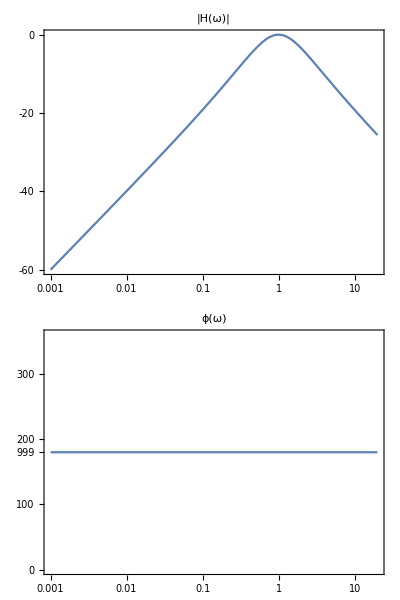

```mathematica
(*Transfer Functions for a simple RCL series circuit*)
(*There are three transfer functions for this circuit depending on which component Subscript[V, 0] is taken across*)

ZR = R;(*Input["Enter The Value Of Resistance:"]*)
ZC = 1/(s C);(*Input["Enter The Value Of Capacitance:"]*)
ZL=s L;(*Input["Enter The Value Of Inductance:"]*)

HS1 = ZR/(ZR + ZC +ZL)//Simplify;(*Resistor Voltage*)
HS2 = ZC/(ZR + ZC+ ZL)//Simplify;(*Cap Voltage*)
HS3 = ZL/(ZR+ZC+ZL)//Simplify;(*Inductor Voltage*)
Hω1 = HS1/.s->ⅉ ω;
Hω2=HS2/.s->ⅉ ω;
Hω3 = HS3 /.s->ⅉ ω;

testParameters={R->1,C->1,L->1};
TableForm[{{HS1,HS2,HS3},{Hω1,Hω2,Hω3}}, TableHeadings->{{"H(s)","H(ω)"},{"R","C","L"}},TableAlignments->{Center, Center}]
StringTemplate["Bode Plot H(ω)_R:"][]
eqn1=Denominator[HS1]==0
pole1 = s/.Solve[eqn1/.testParameters,s][[1]]//N
pole2 = s/.Solve[eqn1/.testParameters,s][[2]]//N
wc=1/(√(L C))/.testParameters
Limit[HS1/.testParameters,s->0]
Limit[HS1/.testParameters,s->∞]
Limit[HS1/.testParameters,s->1]
BodePlot[Hω1/.testParameters,PlotLabel->{"|H(ω)|","ϕ(ω)"}]
```